```mathematica
ValueThumbSlider[v_]:=ValueThumbSlider[v,{0,1}];
ValueThumbSlider[Dynamic[var_],{min_,max_},options___]:=LocatorPane[Dynamic[If[!NumberQ[var],var=min];{var,0},(var=First[#])&],
Graphics[{AbsoluteThickness[1.5],Line[{{min,0},{max,0}}],
Dynamic[{Text[var,{var,0},{0,-1}],Polygon[{Offset[{0,-1},{var,0}],Offset[{-5,-8},{var,0}],Offset[{5,-8},{var,0}]}]}]},
ImageSize->{300,30},PlotRange->{{min,max}+0.1{-1,1}(max-min),{-1,1}},AspectRatio->1/10],
{{min,0},{max,0}},Appearance->None];
ValueThumbSlider[Dynamic[var_],{min_,max_,scale_},options___]:=LocatorPane[Dynamic[If[!NumberQ[var],var=min];{var,0},(var=First[#])&],
Graphics[{AbsoluteThickness[1.5],Line[{{min,0},{max,0}}],
Dynamic[{Text[var,{var,0},{0,-1}],Polygon[{Offset[{0,-1},{var,0}],Offset[{-5,-8},{var,0}],Offset[{5,-8},{var,0}]}]}]},
ImageSize->{300,30},PlotRange->{{min,max}+0.1{-1,1}(max-min),{-1,1}},AspectRatio->1/10],
{{min,0},{max,0},{scale,0}},Appearance->None];
```

# The Normal Distribution

```mathematica
Clear[μ,σ];
PDF[NormalDistribution[μ,σ],t]
```

(ⅇ^(-(t-μ)^2/(2 σ^2)))/(√(2 π) σ)

## The relationship to the error Function

```mathematica
FullSimplify[Integrate[ PDF[NormalDistribution[μ,σ], t],{t,x0,x}]]
FullSimplify[Integrate[ A PDF[NormalDistribution[μ,σ],a t],{t,x0,x}]]
FullSimplify[Integrate[ A PDF[NormalDistribution[μ,σ] ,t],{t,sMin,sMax}]]
```

1/2 (Erf[(x-μ)/(√2 σ)]-Erf[(x0-μ)/(√2 σ)])

(A (-Erf[(-a x+μ)/(√2 σ)]+Erf[(-a x0+μ)/(√2 σ)]))/(2 a)

1/2 A (Erf[(sMax-μ)/(√2 σ)]-Erf[(sMin-μ)/(√2 σ)])

```mathematica
g[sMax_,sMin_, σ_]:= (sMax-sMin)/(Sqrt[2] σ)
```

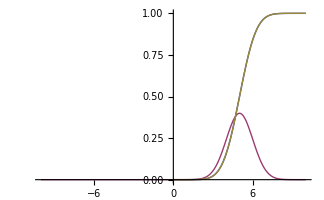

```mathematica
μ =5;
σ =1;
sMax = 10; sMin = 0;
g =  (sMax-sMin)/(Sqrt[2] σ) ;
c = μ;
dRange =N[ 1/2 (Erf[(μ - sMin)/(√2 σ)]+Erf[(sMax - μ)/(√2 σ)])];
dMin = 0;
dMax = dMin + dRange;
setUprErf[ g,c,sMin,sMax,dMin,dMax]
Plot[{1/2 (Erf[(x-μ)/(√2 σ)]+Erf[μ/(√2 σ)]),PDF[NormalDistribution[μ,σ],x], nErf[x]},{x,-10,10},PlotRange->{Automatic,{0,1}}]
```

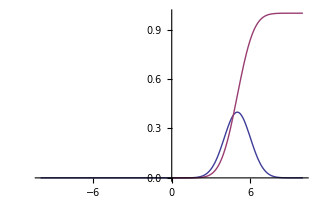

```mathematica
Plot[{PDF[NormalDistribution[μ,σ],x], nErf[x]},{x,-10,10},PlotRange->{Automatic,{0,1}}]
```

```mathematica
Clear[μ,σ, g,c, sMin, sMax, dMin, dMax];
Expand[Log[1/2 (Erf[(μ - sMin)/(√2 σ)]+Erf[(sMax - μ)/(√2 σ)])]]
```

Log[1/2 (Erf[(sMax-μ)/(√2 σ)]+Erf[(-sMin+μ)/(√2 σ)])]

```mathematica
dMax
```

```mathematica
g[σ
```

0.999999

```mathematica
nErf[h]
```

(255 Erf[3/85])/(Erf[3/85]+Erf[82/85])+(255 Erf[82/85])/(Erf[3/85]+Erf[82/85])

```mathematica
nErf[x] /.{Erf[(g (c-x))/(sMax-sMin)]->- Erf[(g (x-c))/(sMax-sMin)]}
%[[0]][%[[1]],Simplify[Together[%[[0]][%[[2]],%[[3]]]]]]
```

dMin+((dMax-dMin) Erf[(g (c-sMin))/(sMax-sMin)])/(Erf[(g (-c+sMax))/(sMax-sMin)]+Erf[(g (c-sMin))/(sMax-sMin)])+((dMax-dMin) Erf[(g (-c+x))/(sMax-sMin)])/(Erf[(g (-c+sMax))/(sMax-sMin)]+Erf[(g (c-sMin))/(sMax-sMin)])

dMin+((dMax-dMin) (Erf[(g (c-sMin))/(sMax-sMin)]+Erf[(g (-c+x))/(sMax-sMin)]))/(Erf[(g (-c+sMax))/(sMax-sMin)]+Erf[(g (c-sMin))/(sMax-sMin)])

```mathematica
FullSimplify[nErf[x] /.{Erf[(g (c-x))/(sMax-sMin)]->- Erf[(g (x-c))/(sMax-sMin)]},TransformationFunctions->{Automatic}]
```

(dMin (Erf[(g (-c+sMax))/(sMax-sMin)]+Erf[(g (c-x))/(sMax-sMin)])+dMax (Erf[(g (c-sMin))/(sMax-sMin)]+Erf[(g (-c+x))/(sMax-sMin)]))/(Erf[(g (-c+sMax))/(sMax-sMin)]+Erf[(g (c-sMin))/(sMax-sMin)])

```mathematica
setUprErf[ g,c,sMin,sMax,dMin,dMax]
nErf[x] /.{Erf[(g (c-x))/(sMax-sMin)]->- Erf[(g (x-c))/(sMax-sMin)]};
%[[0]][%[[1]],Simplify[Together[%[[0]][%[[2]],%[[3]]]]]]
```

dMin+((dMax-dMin) (Erf[(g (c-sMin))/(sMax-sMin)]+Erf[(g (-c+x))/(sMax-sMin)]))/(Erf[(g (-c+sMax))/(sMax-sMin)]+Erf[(g (c-sMin))/(sMax-sMin)])

```mathematica
FullSimplify[Integrate[PDF[NormalDistribution[0,1],t],{t,0,x}]]
```

1/2 Erf[x/(√2)]

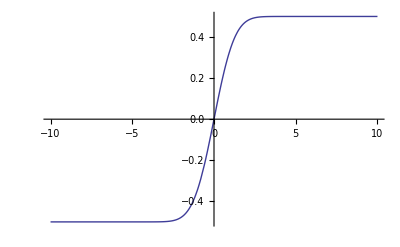

```mathematica
Plot[1/2 Erf[x/(√2)],{x,-10,10}]
```

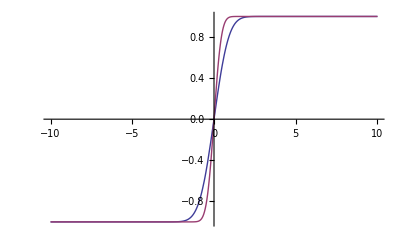

```mathematica
Plot[{Erf[x],Erf[2 x]},{x,-10,10}]
```

```mathematica
mErf[x_, g_,c_]:=1/2 ( Erf[g (x -c)]+1)
InputForm[FullSimplify[(yMax-yMin)(mErf[x,g/(xMax-xMin),c]-mErf[xMin,g/(xMax-xMin),c])/(mErf[xMax,g/(xMax-xMin),c]-mErf[xMin,g/(xMax-xMin),c])+yMin, xMin <=c≤xMax]]
```

yMin + ((-yMax + yMin)*(Erf[(g*(-c + x))/(xMax - xMin)] + Erf[(g*(c - xMin))/(xMax - xMin)]))/(Erf[(g*(c - xMax))/(xMax - xMin)] + Erf[(g*(-c + xMin))/(xMax - xMin)])

```mathematica
aErf[x_, g_,c_,xMin_,xMax_,yMin_,yMax_,erf_:Function[{a,b},Erf[a,b]]]:=yMin+((yMax-yMin)*(Piecewise[{{erf[(g*(-c+x)),(xMax-xMin)],x≥c},{-erf[(g*(c-x)),(xMax-xMin)],x<c}}]+erf[(g*(c-xMin)),(xMax-xMin)]))/( erf[(g*(-c+xMax)),(xMax-xMin)]+erf[(g*(c-xMin)),(xMax-xMin)]);
```

```mathematica
aErf[x, g,c,xMin,xMax,yMin,yMax]
```

yMin+((yMax-yMin) (Erf[g (c-xMin),xMax-xMin]+(Piecewise[{{Erf[g (-c+x),xMax-xMin], x≥c}, {-Erf[g (c-x),xMax-xMin], x<c}, {0, True}}])))/(Erf[g (-c+xMax),xMax-xMin]+Erf[g (c-xMin),xMax-xMin])

```mathematica
Clear[setUprErf];
setUprErf[ g_,c_,sMin_,sMax_,dMin_,dMax_]:=Module[{aa5,aa4,aa3,aa2,aa1,ppD,ppN},
Clear[shift,scale,dRange,sRange, ErfA,ErfB, grad,con,ErfA,ErfB,iErf];
grad= g;
con = c;
dRange = dMax-dMin;
sRange = sMax-sMin;
ErfA = Erf[g (c-sMin)/sRange];
ErfB = Erf[g (-c+sMax)/sRange]+Erf[g (c-sMin)/sRange];
     shift=dRange*ErfA/ErfB + dMin;
     scale=dRange/ErfB;
maxStep = (2  grad scale)/(Sqrt[π] sRange);
iErf[x_]:=Evaluate[ Floor[N[shift]] +Floor[N[scale]]  Erf[((grad*(x-con))/sRange)]];
nErf[x_]:=Evaluate[ shift +scale  Erf[((grad*(x-con))/sRange)]];
]
```

```mathematica
Clear[g,c]
setUprErf[ g,c,sMin,sMax,dMin,dMax]
Together[iErf[x]]
Together[nErf[x]]
```

Erf[(g (-c+x))/(sMax-sMin)] Floor[(dMax-1. dMin)/(Erf[(g (-1. c+sMax))/(sMax-1. sMin)]+Erf[(g (c-1. sMin))/(sMax-1. sMin)])]+Floor[dMin+((dMax-1. dMin) Erf[(g (c-1. sMin))/(sMax-1. sMin)])/(Erf[(g (-1. c+sMax))/(sMax-1. sMin)]+Erf[(g (c-1. sMin))/(sMax-1. sMin)])]

(dMin Erf[(g (-c+sMax))/(sMax-sMin)]+dMax Erf[(g (c-sMin))/(sMax-sMin)]+dMax Erf[(g (-c+x))/(sMax-sMin)]-dMin Erf[(g (-c+x))/(sMax-sMin)])/(Erf[(g (-c+sMax))/(sMax-sMin)]+Erf[(g (c-sMin))/(sMax-sMin)])

```mathematica
setUprErf[ 1.4138,188,0,255,0,255]
TableForm[{{"ErfA", "ErfB", "shift", "scale"},{ErfA, ErfB, shift, scale},{N[ErfA], N[ErfB], N[shift],N[ scale]}}]
iErf[a]
N[iErf[128]]
```

ErfA | ErfB | shift | scale
0.85954 | 1.26019 | 173.928 | 202.35
0.85954 | 1.26019 | 173.928 | 202.35

173+202 Erf[0.00554431 (-188+a)]

99.8827

```mathematica
Clear[ g,c,sMin,sMax,dMin,dMax]
Clear[dRange,sRange, ErfA,ErfB, grad,con,ErfA,ErfB,iErf]
D[ shift +scale  Erf[((grad*(x-con))/sRange)],x]
```

(2 ⅇ^(-(grad^2 (-con+x)^2)/sRange^2) grad scale)/(√π sRange)

```mathematica
nf4Tn12Bb5
```

```mathematica
Manipulate[
DiscretePlot[{Evaluate[setUprErf[ g,c,sMin,sMax,dMin,dMax]];Floor[iErf[x]]},{x,sMin,sMax},PlotStyle->{Blue},AxesLabel->TraditionalForm/@{a,iErf[a]},PlotRange->{{sMin,sMax},{dMin, dMax}},Filling->Bottom,
Epilog->{Red,Dashing[{.02,.02}],Line[{{sMin,dMax},{sMax,dMax}}], Line[{{sMin,dMin},{sMax,dMin}}]}],
{{dMin,0},-255,255,1,ValueThumbSlider[##]&},{{dMax,255},1,255,1,ValueThumbSlider[##]&},{sMin,0,sMax,1,ValueThumbSlider[##]&},{{sMax,255},1,255,1,ValueThumbSlider[##]&},{{c,188},sMin,sMax,1,ValueThumbSlider[##]&},{{g,1.4138},1,10,ValueThumbSlider[##]&}
]
```

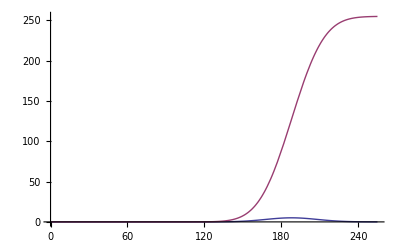

```mathematica
μ =188;
σ =20.1188;
sMax = 255; sMin = 0;
g =  (sMax-sMin)/(Sqrt[2] σ) ;
c = μ;
dRange =255; dMin = 0; dMax = dMin + dRange;
setUprErf[ g,c,sMin,sMax,dMin,dMax]
Plot[{dRange PDF[NormalDistribution[μ,σ],x], nErf[x]},{x,sMin,sMax},PlotRange->{{sMin,sMax},{dMin,dMax}}]
```